# Non-Linear Dynamics

```mathematica
ArrayPlot[CellularAutomaton[90,{{1},0},127]]
```

-Graphics-

## Logistic Map

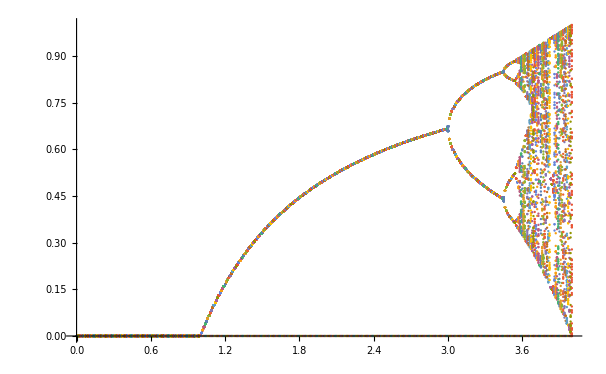

```mathematica
ListPlot[Table[Thread[{r,Nest[r # (1-#)&,Range[0,1,0.01],1000]}],{r,0,4,0.01}]]
```

## Julia Sets

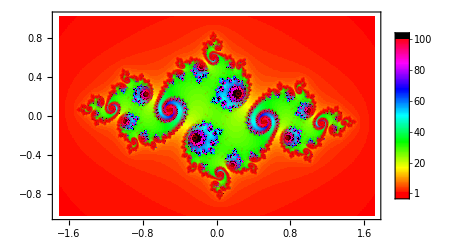

```mathematica
JuliaSetPlot[(-0.77+0.12 ⅈ)+z^2,z,ColorFunction->Hue, PlotStyle->Opacity[.2, Red],PlotLegends->Automatic]
```

## Mandelbrot Set

```mathematica
MandelbrotSetPlot[{-0.65+0.47 I,-0.4+.7I},PlotLegends->Automatic]
```

-Graphics-

```mathematica
Cosh(0)
```

0

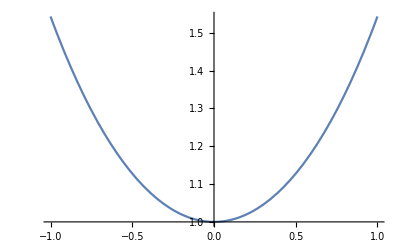

```mathematica
Plot[Cosh[x], {x, -1 ,1}]
```

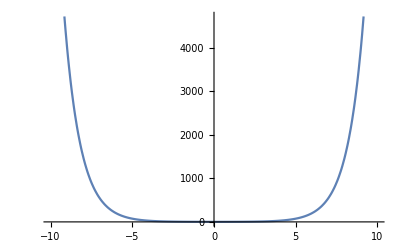

```mathematica
Plot[Cosh[x], {x, -10, 10}]
```

```mathematica
Roots[Cosh[x]==0,x]
```

Roots::neq: Cosh[x] is expected to be a polynomial in the variable x.

```mathematica
NSolve[Cosh[x]==0,x] //Simplify
```

{{x→ConditionalExpression[(0.-1.5708 ⅈ)+(0.+6.28319 ⅈ) C[1],C[1]∈Integers]},{x→ConditionalExpression[(0.+1.5708 ⅈ)+(0.+6.28319 ⅈ) C[1],C[1]∈Integers]}}